```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[] <> "\\Code\\Output"];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\gerce\Documents\WORK DIRECTORY\Курсовая работа 6 сем\КОД\дополнительно\\Code\Output.

# Визуализация численного решения линейного одномерного уравнения переноса

## Тест №3 “Прямоугольник”

## Получение аналитического решения

```mathematica
(* Объявление задачи *)
eq = D[u[x, t], t] + a D[u[x, t], x] == 0;
l1 = -1;
l2 = 1;
u0[x_]=  1/3(1-Cos[ (2π(x-l1))/(l2- l1)]);
ic = u[x, 0] == u0[x];
sol4= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]
L1 = -1;
L2 = 1;
```

1/3 (1-Cos[π (1-a (t-x/a))])

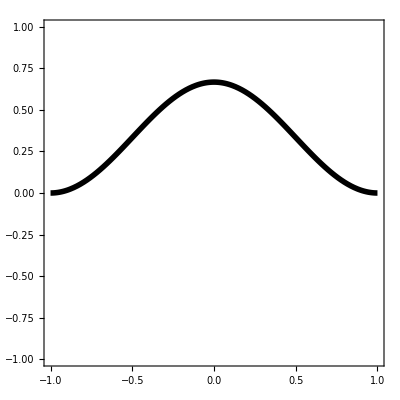

```mathematica
LTEdataAnalPlot[sol_, time_]:= Module[{solplot,plotrange},
plotrange = {{-1, 1}, {-1, 1}};

solplot = Plot[Evaluate[sol/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->plotrange,
 AspectRatio -> 1,
Axes -> True,
Frame->True,
FrameTicks-> None,
AxesOrigin -> {0,0},
PlotPoints -> 100,
PlotStyle->{Black,Thickness[0.01]}

];
solplot
]
LTEdataAnalPlot[sol4, 0]
```

## Импорт данных численного решения

```mathematica
data41 = Import["test4\\test4_LD2e.txt", "Table"];
data42= Import["test4\\test4_Lax.txt", "Table"];
data43 = Import["test4\\test4_LaxWen.txt", "Table"];
data44 = Import["test4\\test4_LD2i.txt", "Table"];
data45 = Import["test4\\test4_LD3e.txt", "Table"];
data46 = Import["test4\\test4_LD3i.txt", "Table"];
```

Import::nffil: File test4\test4_LD2e.txt not found during Import.

Import::nffil: File test4\test4_Lax.txt not found during Import.

Import::nffil: File test4\test4_LaxWen.txt not found during Import.

Import::nffil: File test4\test4_LD2i.txt not found during Import.

Import::nffil: File test4\test4_LD3e.txt not found during Import.

Import::nffil: File test4\test4_LD3i.txt not found during Import.

## Модуль для визуализации численного решения

```mathematica
LTEPlot[data_, ifjoin_: False, text_ : ""]:= Module[{plotdata},
plotdata = Manipulate[ListPlot[Table[{data[[1]][[x]],data[[t]][[x]]}, {x, 2, Length@data[[t]]-1}
], Joined->ifjoin, PlotRange->{{-1, 1},{-1, 1}}, AxesLabel->{"x", "u(x, t)"}, PlotLabel-> text],{t, 2,Length@data, 1}]
]
```

## Результаты работы программы

```mathematica
LTEPlot[data41, False, "Явная схема с левой разностью 1-го пор."]
(*LTEPlot[data42, False, "Схема Лакса"]
LTEPlot[data43, False, "Схема Лакса-Вендрофа"]
LTEPlot[data44, False,"Неявная схема с левой разностью 1-го пор."]
LTEPlot[data45, False, "Явная схема с левой разность 2-го пор."]
LTEPlot[data46, False,"Неявная схема с левой разностью 2-го пор."]*)
```

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

```mathematica
LTEdataNumPlot[data_, time_]:= Module[{solplot,plotrange},
plotrange = {{-1, 1}, {-1, 1}};

solplot = ListPlot[Table[{data[[1]][[x]],data[[time]][[x]]}, {x, 2, Length@data[[time]]-1}
], Joined->False, PlotRange->plotrange,
 AspectRatio -> 1,
Axes -> True,
Frame->True,
FrameTicks-> None,
AxesOrigin -> {0,0},
PlotStyle->Black,
PlotMarkers->{Automatic,0.03}

];
solplot
]
```

```mathematica
plot = LTEdataNumPlot[data41, 2]
Export["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\дополнительно\\plot_test4_num.png",plot, ImageSize -> {1500, 1500}];
plot = LTEdataAnalPlot[sol4, 0]
Export["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\дополнительно\\plot_test4_anal.png",plot, ImageSize -> {1500, 1500}];
```

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

```mathematica
q = D[u[x, t], t] + a D[u[x, t], x] == 0;
a = 1;
L1 = -10;
L2 = 10;
T = 1;
(* 1. Левый треугольник *)
l1 = -1;
l2 = 1;
u0[x_]=  (x-l1)/(l2-l1);
ic = u[x, 0] == u0[x];
sol1= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]

(* 2. Правый треугольник *)
l1 = -1;
l2 = 1;
u0[x_]=  (l2-x)/(l2-l1);
ic = u[x, 0] == u0[x];
sol2 = DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]

(* 3. Прямоугольник *)
u0[x_]=  2/3;
ic = u[x, 0] == u0[x];
sol3= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]

(* 4. Косинус *)
l1 = -1;
l2 = 1;
u0[x_]=  1/3(1-Cos[ (2π(x-l1))/(l2- l1)]);
ic = u[x, 0] == u0[x];
sol4= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]
(* 5. Зуб *)
l1 = -0.2;
l2 = 0.2;
l11 = -0.1;
l22 = 0.1; 
u0[x_]=  Piecewise[{{-2/3(l11 - l1)(x-l1) + 1, l1 <=x<l11 },
{1/3, l11<=x<=l22 }, 
{2/3(l2 - l22)(x-l2) + 1, l22 <x<=l2 }}];
ic = u[x, 0] == u0[x];
sol5= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]
```

1/2 (1-t+x)

1/2 (1+t-x)

2/3

1/3 (1-Cos[π (1-t+x)])

Piecewise[{{0.0133333 (74.+5. t-5. x), -0.2≤-1. t+x<-0.1}, {0.333333, -0.1≤-1. t+x≤0.1}, {0.0133333 (74.-5. t+5. x), 0.1<-1. t+x≤0.2}, {0., True}}]

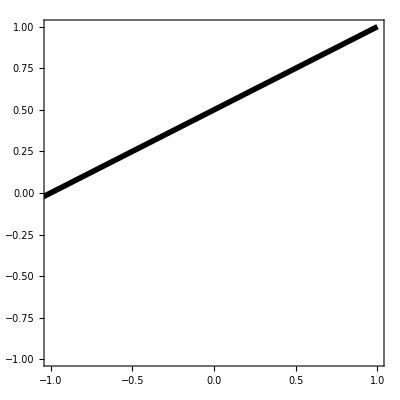

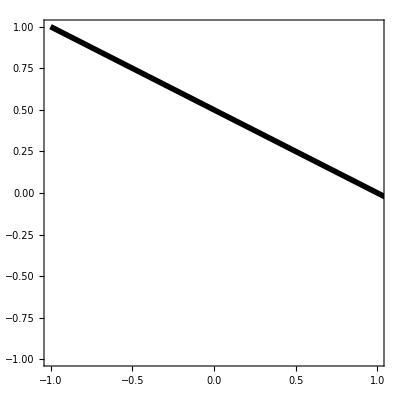

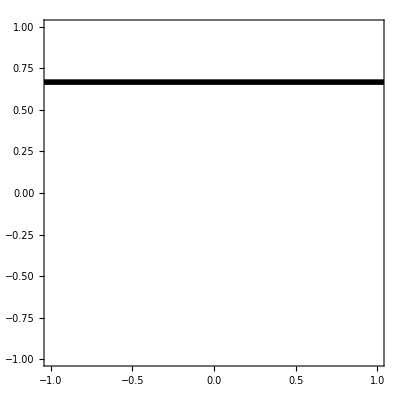

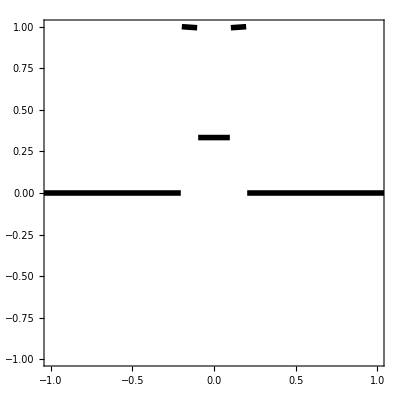

```mathematica
plot = LTEdataAnalPlot[sol1, 0]
Export["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\дополнительно\\plot_test1_anal.png",plot, ImageSize -> {1500, 1500}];
plot = LTEdataAnalPlot[sol2, 0]
Export["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\дополнительно\\plot_test2_anal.png",plot, ImageSize -> {1500, 1500}];
plot = LTEdataAnalPlot[sol3, 0]
Export["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\дополнительно\\plot_test3_anal.png",plot, ImageSize -> {1500, 1500}];
plot = LTEdataAnalPlot[sol5, 0]
Export["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\дополнительно\\plot_test5_anal.png",plot, ImageSize -> {1500, 1500}];
```